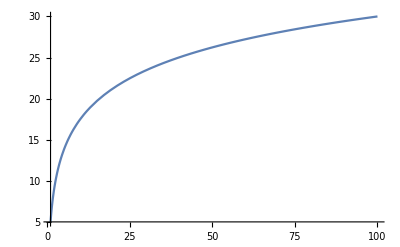

```mathematica
Plot[25/4.605170185988092Log[x]+5-5Log[5]/Log[5],{x,1,100}]
```

```mathematica
Log[100]
```

Log[100]

```mathematica
N[Log[100]]
```

4.60517

```mathematica
100/%
```

21.7147

```mathematica
25/4.605170185988092Log[40]
```

20.0257

```mathematica
Log[0]
```

-∞

```mathematica
Log[1]
```

0

```mathematica
Remove["Global`*"]
f[x_]:= (x+b)^(0.5)+c 
FullSimplify[Solve[{f[0]==min, f[100]==max},{b,c}]]
```

{{b→-50.+0.25 max^2-0.5 max min+0.25 min^2+2500./(1. max^2-2. max min+1. min^2),c→0.5 max+0.5 min+(0.-50. max+50. min)/(1. max^2-2. max min+1. min^2)}}

{{b→-50.+0.25 max^2-0.5 max min+0.25 min^2+2500./(1. max^2-2. max min+1. min^2),c→0.5 max+0.5 min+(0.-50. max+50. min)/(1. max^2-2. max min+1. min^2)}}

```mathematica
{{b->(0.25 max^4-1. max^3 min val+max^2 (-50.+1.5 min^2) val^2+max min (100.-1. min^2) val^3+(2500.-50. min^2+0.25 min^4) val^4)/(1. max val-1. min val^2)^2,c->(0.5 max^2+(-50.-0.5 min^2) val^2)/(val (1. max-1. min val))}}
```

{{1→410.545,c→-19.2619}}

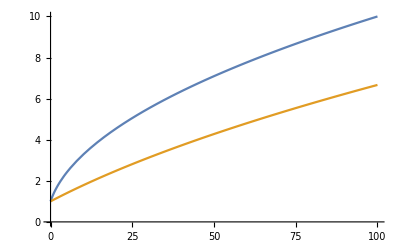

```mathematica
b=1;
min=1;
max=10;
val=1.5;
b1=-50.00000000000001+0.25 max^2-0.5 max min+0.25 min^2+2500./(1. max^2-2. max min+1. min^2);
c1=0.5 max+0.5 min+(0.-50. max+50. min)/(1. max^2-2. max min+1. min^2);
b2=(0.25 max^4-1. max^3 min val+max^2 (-50.+1.5 min^2) val^2+max min (100.-1. min^2) val^3+(2500.-50. min^2+0.25 min^4) val^4)/(1. max val-1. min val^2)^2;
c2 = (0.5 max^2+(-50.-0.5 min^2) val^2)/(val (1. max-1. min val));
Plot[{(x+b1)^(0.5)+c1,(x+b2)^(0.5)+c2},{x,0,100}]
```

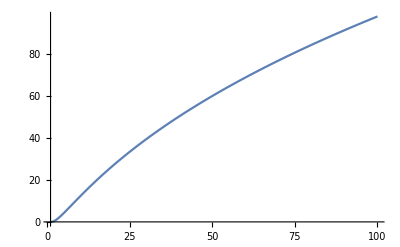

```mathematica
f1[x_]:=Log[x]
Plot[f1[x]^3,{x,1,100}]
```

Log

StartExternalSession::noinstall: No valid installations for system Python were found with the options specified.

$Failed

```mathematica
?Log
```

Log[z] gives the natural logarithm of z (logarithm to base e). 
Log[b,z] gives the logarithm to base b.

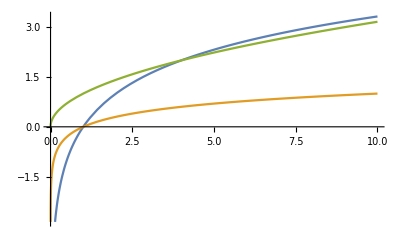

```mathematica
Plot[{Log[2,x],Log[10,x],x^(0.5)},{x,0,10}]
```

```mathematica
?Root
```

Root[f,k] represents the exact k^th root of the polynomial equation f[x]==0. 
Root[{f_1,f_2,…},{k_1,k_2,…}] represents the last coordinate of the exact vector {a_1,a_2,…} such that a_i is the k_i^th root of the polynomial equation f_i[a_1,…,a_(i-1),x]==0.
Root[{f,x_0}] represents the exact root of the general equation f[x]==0 near x=x_0.
Root[{f,x_0,n}] represents n roots of the equation f[x]==0 near x=x_0.

```mathematica
Remove["Global`*"]
Solve[{min==c,max==a(100)^(2/3)+c},{a,c},Reals]
```

{{a→max/(10 10^(1/3))-min/(10 10^(1/3)),c→min}}

1

10

2

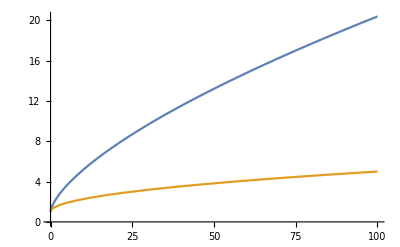

```mathematica
min = 1
max = 10
val = 2
Plot[{(max/10-min/10)(x)^(2/3)+min,-((-max+min val)/(10 val))(x)^(1/2)+min},{x,0,100}]
```